```mathematica
Qfield[x_]:=(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])
```

```mathematica
Условия задачи
```

```mathematica
ν=(*1/1000*)10^-5;τ=0.015;eps=0.0001;Vinf={1,0};
```

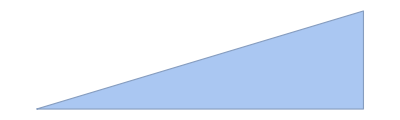

```mathematica
Rdots={{-1,-0.1},(*{0,0.2},*){1,1/2},(*{1,0.2},*){1,-0.1}(*,{0,-0.1}*)};
Rarea=BoundaryMeshRegion[Rdots,Line[{1,2,3,1}]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
rotRsides=RotateLeft@Rsides;
lSides=Table[√(Rsides[[i]].Rsides[[i]]),{i,Length@Rsides}];
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
```

```mathematica
pics={};pics2={};
```

```mathematica
Предварительное составление матрицы и нахождение начальных вихрей
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
curlsOnPanel={};
curlsInFlow={};
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlsOnPanel,{nGammaR[[i]],curlDeploy[[i]]}]];
minCurl=Max[Abs@nGammaR]*0.001;
```

```mathematica
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
```

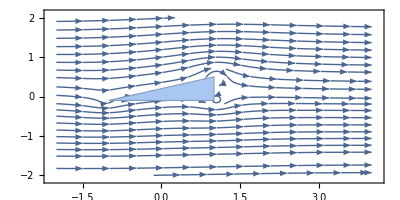

```mathematica
Show[StreamPlot[Vfield,{x,-2,4},{y,-2,2}],Rarea,AspectRatio->1/2]
```

```mathematica
For[k=0,k<200,k++,
AllCurls=Join[curlsInFlow,curlsOnPanel];
f1=ParallelTable[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@AllCurls[[m]]]First@AllCurls[[m]],{m,1,Length@AllCurls}],{i,1,Length@curlDeploy}];
solution=Solve[{L1.newGamma+r==-f0-f1,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@curlsOnPanel,i++,
If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/16,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]];
curlsOnPanel[[i]][[2]]=(Last@curlsOnPanel[[i]]*First@curlsOnPanel[[i]]+curlDeploy[[i]]*nGammaR[[i]])/(First@curlsOnPanel[[i]]+nGammaR[[i]]),
 AppendTo[curlsInFlow,curlsOnPanel[[i]]];(*слабое место, переделать!!!!*)
curlsOnPanel[[i]][[1]]=nGammaR[[i]];
curlsOnPanel[[i]][[2]]=curlDeploy[[i]];
]
(*If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/4,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]]
]*)
];
AllCurls=Join[curlsInFlow,curlsOnPanel];

etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;(*переделать в соответствии с диссером*)
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@(AllCurls[[i]]),{i,Length@AllCurls}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@AllCurls}];
I2=-Parallelize@Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I1=Parallelize@Sum[First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I3=-Parallelize@Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
(*I3=-Parallelize@Sum[Rnormals[[i]]eps (1-Exp[-(√(Rsides[[i]].Rsides[[i]]))/(2 eps)]),{i,Length@Rnormals}];*)
I0=2π eps^2+Parallelize@Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]]lSides[[i]],{i,Length@Rnormals}];
Wfield=ν(-I2/I1+I3/I0);
If[Length@curlsInFlow>0,
curlsInFlow=ParallelTable[{First@curlsInFlow[[i]],Last@(curlsInFlow[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsInFlow[[i]])+eps/1000,y->Last@Last@(curlsInFlow[[i]])+eps/1000}},{i,Length@curlsInFlow}];]
curlsOnPanel=ParallelTable[{First@curlsOnPanel[[i]],Last@(curlsOnPanel[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsOnPanel[[i]])+eps/1000,y->Last@Last@(curlsOnPanel[[i]])+eps/1000}},{i,Length@curlsOnPanel}];

(*Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}*)
(*
curlsOnPanel={};
curlsInFlow={};*)
(*Определяем кандидатов под аннигиляцию и, пока есть такая возможность, без угрызений совести выпиливаем из списка*)
(*curlsToRemove={};*)
For[i=1,i≤Length@curlsOnPanel,i++,If[RegionMember[Rarea,Last@(curlsOnPanel[[i]])] ||Abs@ First@(curlsOnPanel[[i]])<minCurl,curlsOnPanel[[i]][[2]]=curlDeploy[[i]];curlsOnPanel[[i]][[1]]=nGammaR[[i]];];];
(*curlsOnPanel=Delete[curlsOnPanel,curlsToRemove];*)
curlsToRemove={};
For[i=1,i≤Length@curlsInFlow,i++,If[RegionMember[Rarea,Last@(curlsInFlow[[i]])] ||Abs@ First@(curlsInFlow[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlsInFlow=Delete[curlsInFlow,curlsToRemove];
AllCurls=Join[curlsInFlow,curlsOnPanel];

Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
If[Mod[k,5]==0,
AppendTo[pics2,Show[(*ContourPlot[Vfield.Vfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];
CurlsGraph=Table[Graphics[{White,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
AppendTo[pics,Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]];]]
```

```mathematica
curlsInFlow
curlsOnPanel
```

{{-2.17321,{2.73341,1.05305}},{1.0039,{1.72844,0.151219}},{-0.371745,{3.2472,1.16966}},{-0.489037,{3.05953,1.3046}},{-0.536711,{3.16118,1.42677}},{0.489317,{1.56344,-0.151229}},{-0.770776,{3.22752,0.79886}},{0.412195,{1.75747,0.577123}},{0.43637,{1.84318,0.874542}},{0.513996,{2.04145,0.717217}},{-1.65207,{0.887836,1.17057}},{0.780867,{1.98538,0.0281384}},{-0.906385,{1.07179,0.0727807}},{0.303582,{1.79969,-0.31882}}}

{{0.0297945,{-0.998673,-0.0958114}},{-1.77783,{1.09734,0.584924}},{1.62225,{0.999591,-0.156275}}}

```mathematica
Length@curlsOnPanel
```

3

```mathematica
Length@pics
```

40

```mathematica
Export["tester2.gif",pics2]
```

tester2.gif

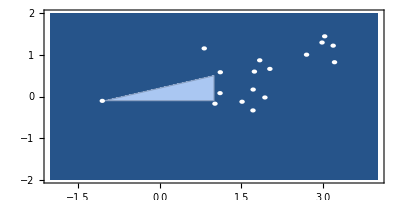

```mathematica
Last@pics
```

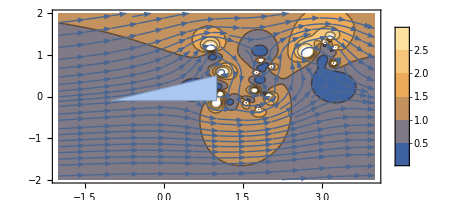

```mathematica
Show[ContourPlot[√(Vfield.Vfield),{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```